```mathematica
Clear["Global`*"]
img = CurrentImage[];
face = FindFaces[img][[1]];
grayface = ColorConvert[img,"Grayscale"];
cropface =ImageResize[ImageTake[grayface,face[[1]],face[[2]]],{75,130}]
Export["Face.jpg",cropface]
DeviceClose["Camera"]
```

Rectangle[{150.5,56.5},{215.5,153.5}]

-Graphics-

Face.jpg

```mathematica
MyFace = Import["Face.jpg"];
signal=Play[Sin[340 2 Pi  t] + Sin[345 2 Pi  t],{t,0,2}];


errors = {}

dev = DeviceOpen["Camera"]
Dynamic[img]

For[i = 0,i<10,i ++,
(* img = Import["D:\\Aarya\\code\\ascii-art-folder\\sentprof.JPG"];  *)
 img = CurrentImage[]; 
faces = FindFaces[img];
print[Length[faces]];
For[j=1, j<=Length[faces],j++,
greyimg = ColorConvert[img,"Grayscale"];
Pause[0.1];
facePerson = ImageResize[ImageTake[greyimg,faces[[j]][[1]],faces[[j]][[2]]],{75,130}];
error = Total[Flatten[ImageData[ImageDifference[MyFace,facePerson]]]];
If[error > 1000, EmitSound[signal];img = HighlightImage[img,faces[[j]]];, Print["Aarya"];];
AppendTo[errors,error]
];

]
DeviceClose[dev]
```

{}

DeviceObject[…]

Aarya

Aarya

Aarya

«7 more identical outputs»

```mathematica
errors
```

{200.733,1284.43,263.863,1291.72,242.643,1260.11,192.49,1275.35,235.584,1298.15,188.694,1282.64,235.784,1256.85,229.706,1243.27,264.263,1302.68,278.298,1304.85}

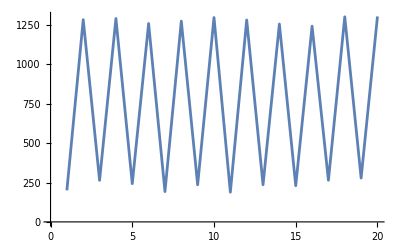

```mathematica
ListLinePlot[errors]
```